交流计算

1、三相相电压

```mathematica
U = 220/220;
f = 50;
w = 2 Pi f;
uAN=Sqrt[2]*U*Cos[w t];
uBN=Sqrt[2]*U*Cos[w t-120*Pi/180];
uCN=Sqrt[2]*U*Cos[w t+120*Pi/180];
uN = uAN+uBN+uCN
```

√2 Cos[100 π t]-√2 Sin[π/6-100 π t]-√2 Sin[π/6+100 π t]

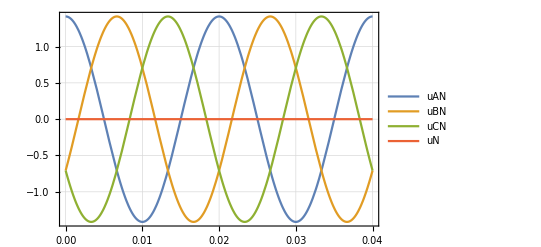

```mathematica
Plot[{uAN,uBN,uCN,uN},{t,0,0.04},Frame->True,GridLines->Automatic,PlotLegends->"Expressions"]
```

## 2、三相线电压

```mathematica
uAB = uAN-uBN;
```

```mathematica
uBC=uBN-uCN;
```

```mathematica
uCA = uCN-uAN;
```

线电压波形如下

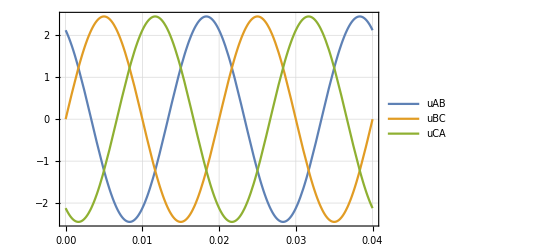

```mathematica
Plot[{uAB,uBC,uCA},{t,0,0.04},Frame->True,GridLines->Automatic,PlotLegends->"Expressions"]
```

## 3、已知线电压计算相电压

如果只有以下三个关系式，是无法根据线电压计算出相电压的。
        uAB = uAN - uBN
        uBC = uBN - uCN
        uCA = uCN - uAN
       三式相加有uAB+uBC+uCA=0，3个线电压上只有2个量独立，无法解出3个未知量Ua、Ub、Uc。       
       -Graphics-
       对于三角形ABC，线电压uAB、uBC、uCA是确定的，但相电压uAN、uBN、uCN不唯一（N为零参考点）， 根源在于零参考点N不确定。
       若再增加一个约束条件：uAN+uBN+uCN=0（零序电压为零），则可以计算出三相电压幅值。
        uAB = uAN - uBN
        uBC = uBN - uCN
        uCA = uCN - uAN
        uAN+uBN+uCN=0
        1、Mathematica根据方程得到结果(约束条件：uAN+uBN+uCN=0)

```mathematica
ux=Solve[uAB==uANx-uBNx && uBC == uBNx-uCNx && uCA==uCNx-uANx  && uANx+uBNx+uCNx==0, {uANx,uBNx,uCNx}];
```

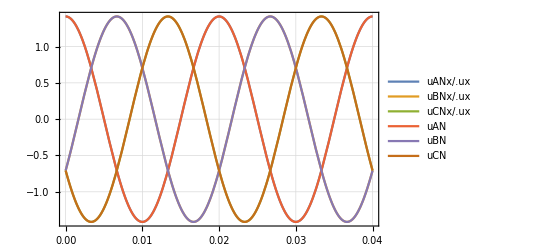

```mathematica
Plot[{uANx /. ux, uBNx /. ux, uCNx /. ux,uAN,uBN,uCN},{t,0,0.04},Frame->True,GridLines->Automatic,PlotLegends->"Expressions"]
```

2、根据三相线电压瞬时值计算出相电压瞬时值(约束条件：uAN+uBN+uCN=0)
                              -Graphics-

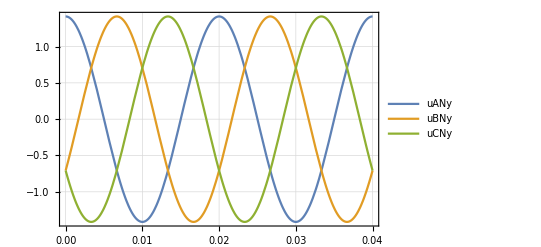

```mathematica
uANy=-(uBC+2uCA)/3;
uBNy=(2*uBC+uCA)/3;
uCNy=(uCA-uBC)/3;
Plot[{uANy, uBNy, uCNy},{t,0,0.04},Frame->True,GridLines->Automatic,PlotLegends->"Expressions"]
```

3、计算三相电压幅值(约束条件：uAN+uBN+uCN=0)
        -Graphics-
                      -Graphics- 
       三相相电压幅值如下(下面计算不对，实际只能用于计算幅值，不能计算瞬时值)

```mathematica
uANz=Sqrt[2(uAB^2+uCA^2)-uBC^2]/3;
uBNz=Sqrt[2(uBC^2+uAB^2)-uCA^2]/3;
uCNz=Sqrt[2(uCA^2+uBC^2)-uAB^2]/3;
```

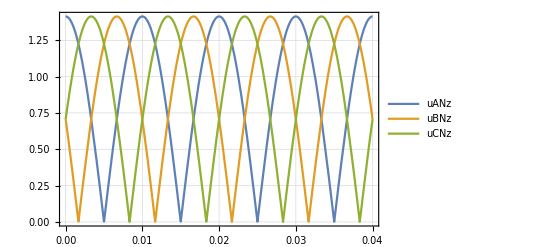

```mathematica
Plot[{uANz, uBNz, uCNz},{t,0,0.04},Frame->True,GridLines->Automatic,PlotLegends->"Expressions"]
```

4、计算三相电压幅值(约束条件：uAN、uBN、uCN夹角为120°)

三相相电压幅值如下

```mathematica
AB=220;
BC=220;
CA=220;
```

```mathematica
(*u1=Solve[uAB==uAN1-uBN1 && uBC == uBN1-uCN1 && uCA==uCN1-uAN1  && uAB^2==uAN1^2+uBN1^2-2 uAN1 uBN1 Cos[2/3 Pi] && uBC^2==uBN1^2+uCN1^2-2 uBN1 uCN1 Cos[2/3 Pi] && uCA^2==uCN1^2+uAN1^2-2 uCN1 uAN1 Cos[2/3 Pi], {uAN1,uBN1,uCN1}]*)
```

```mathematica
u1=Solve[AB^2==AN1^2+BN1^2-2 AN1 BN1 Cos[2/3 Pi] && BC^2==BN1^2+CN1^2-2 BN1 CN1 Cos[2/3 Pi] && CA^2==CN1^2+AN1^2-2 CN1 AN1 Cos[2/3 Pi]&&AN1==BN1&&BN1==CN1 , {AN1,BN1,CN1}]
```

{{AN1→-220/(√3),BN1→-220/(√3),CN1→-220/(√3)},{AN1→220/(√3),BN1→220/(√3),CN1→220/(√3)}}

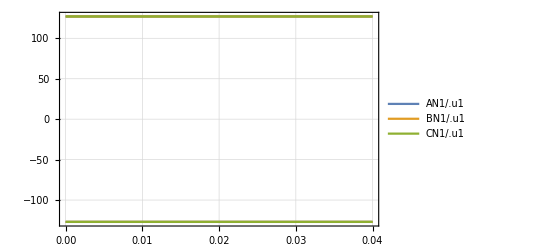

```mathematica
Plot[{AN1 /. u1, BN1 /. u1, CN1 /. u1},{t,0,0.04},Frame->True,GridLines->Automatic,PlotLegends->"Expressions"]
```

4、三相电压的相量表示

旋转算子

```mathematica
rot=E^(I 2/3 Pi)
```

ⅇ^((2 ⅈ π)/3)

三相相电压的相量

```mathematica
UAN=U*0.5+10
UBN=U*rot^2*0.5
UCN=U*rot*2
```

10.5

-0.25-0.433013 ⅈ

2 ⅇ^((2 ⅈ π)/3)

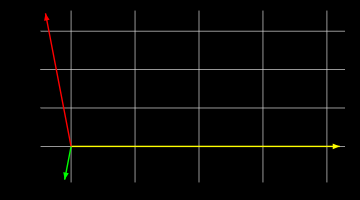

```mathematica
Graphics[{Thick,Yellow,Arrow[{{0,0},{Re[UAN],Im[UAN]}}],Thick,Green,Arrow[{{0,0},{Re[UBN],Im[UBN]}}],Thick,Red,Arrow[{{0,0},{Re[UCN],Im[UCN]}}]},Frame->True,GridLines->Automatic,Background->Black,ImageSize->Medium]
```

三相电压波形

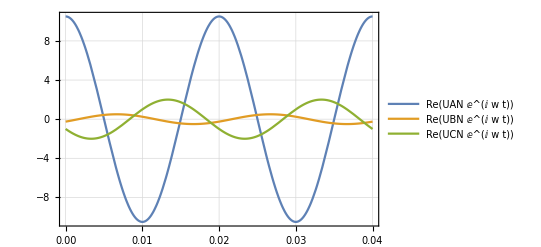

```mathematica
Plot[{Re[UAN*E^(I w t)],Re[UBN*E^(I w t)],Re[UCN*E^(I w t)]},{t,0,0.04},Frame->True,GridLines->Automatic,PlotLegends->"Expressions"]
```

三相线电压的相量

```mathematica
UAB=UAN-UBN
UBC=UBN-UCN
UCA=UCN-UAN
```

10.75+0.433013 ⅈ

0.75-2.16506 ⅈ

-11.5+1.73205 ⅈ

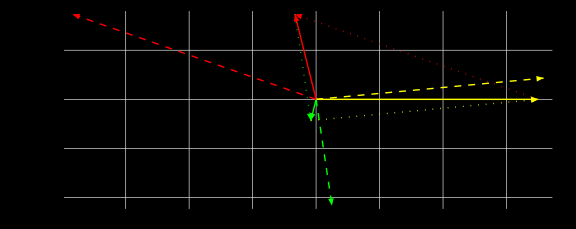

```mathematica
Graphics[{Thick,Yellow,Arrow[{{0,0},{Re[UAN],Im[UAN]}}],Thick,Green,Arrow[{{0,0},{Re[UBN],Im[UBN]}}],Thick,Red,Arrow[{{0,0},{Re[UCN],Im[UCN]}}],Dashed,Thick,Yellow,Arrow[{{0,0},{Re[UAB],Im[UAB]}}],Green,Arrow[{{0,0},{Re[UBC],Im[UBC]}}],Red,Arrow[{{0,0},{Re[UCA],Im[UCA]}}],Dotted,Yellow,Arrow[{{Re[UBN],Im[UBN]},{Re[UAN],Im[UAN]}}],Green,Arrow[{{Re[UCN],Im[UCN]},{Re[UBN],Im[UBN]}}],Red,Arrow[{{Re[UAN],Im[UAN]},{Re[UCN],Im[UCN]}}]},Frame->True,GridLines->Automatic,Background->Black,ImageSize->Large]
```

根据线电压计算相电压

```mathematica
AN=Norm[UAN]
BN=Norm[UBN]
CN=Norm[UCN]
AB=Norm[UAB]
BC=Norm[UBC]
CA=Norm[UCA]
```

10.5

0.5

2

10.7587

2.29129

11.6297

已知线电压幅值，计算出三相电压幅值(约束条件：UAN、UBN、UCN夹角为120°)

```mathematica
u2=Solve[AB^2==AN1^2+BN1^2-2 AN1 BN1 Cos[2/3 Pi] && BC^2==BN1^2+CN1^2-2 BN1 CN1 Cos[2/3 Pi] && CA^2==CN1^2+AN1^2-2 CN1 AN1 Cos[2/3 Pi]&&AN1≥0&&BN1≥0&&CN1≥0, {AN1,BN1,CN1}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{AN1→10.5,BN1→0.5,CN1→2.}}